```mathematica
Integrate[Sec[θ], θ]
```

2 EllipticE[θ/2,2]

```mathematica
ArcSec[1]
```

0

```mathematica
F[ξ_]:=(√(-1+ξ^2))/ξ
```

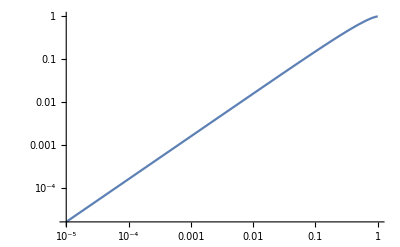

```mathematica
G[ξ_]:= ArcSec[ξ] / ξ
U1[ξ_]:= G[ξ] - G[1] + 1 - F[ξ]
LogLogPlot[U1[1/p], {p,10^-5,1}]
```

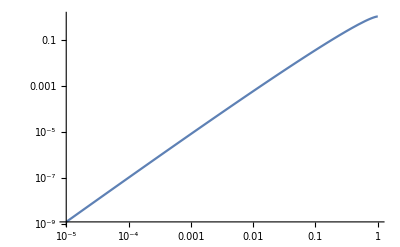

```mathematica
G[ξ_]:= Log[ξ + Sqrt[ξ^2 - 1]] / ξ^2
U1[ξ_]:= G[ξ] - G[1] + 1 - F[ξ]
LogLogPlot[U1[1/p], {p,10^-5,1}]
```

```mathematica
Assuming[α>-2, Integrate[(Sec[θ])^(α), θ]]
```

(Cos[θ]^2)^(-1/2+α/2) Hypergeometric2F1[1/2,(1+α)/2,3/2,Sin[θ]^2] Sec[θ]^(-1+α) Sin[θ]

0.0232766

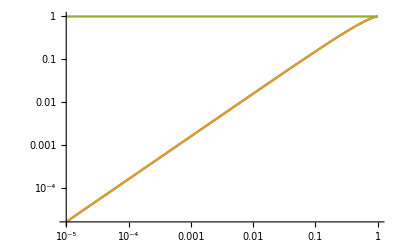

```mathematica
G[ξ_,α_]:=  Hypergeometric2F1[1/2,(3+α)/2,3/2,(ξ^2 - 1) / ξ^2] * Sqrt[ξ^2 - 1]/ξ^(α+4)
U2[ξ_,α_]:= G[ξ,α] - G[ 1,α] + 1 - F[ξ]
U[100,-2.1]
one[ξ_]:= 1
LogLogPlot[{U1[1/p],U2[1/p,-2], one[p]},{p,10^-5,1}]
```

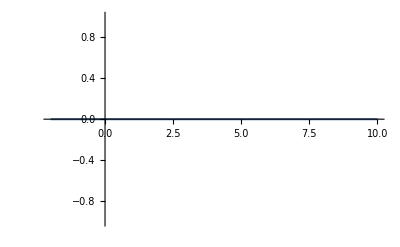

```mathematica
Plot[G[1,α],{α,-2,10}]
```

```mathematica
FortranForm[Simplify[U2[R/p,α]]]
```

1 - (p*Sqrt(-1 + R**2/p**2))/R + 
     -  (p**4*Sqrt(-1 + R**2/p**2)*
     -     Hypergeometric2F1(0.5,(3 + α)/2.,1.5,1 - p**2/R**2))/
     -   (R**4*(R/p)**α)

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression (0\ π\ ComplexInfinity)/2 encountered.